```mathematica
P[x_,z_,kt_,delta_,k_]:=Module[{e2=x,
k0=k,
e1=1.5^2,
e3=z,
d=delta},
  kz[e_,kv_]:=Sqrt[k0^2 *e-kv ^2];


P1=({{(kz[e2,kt]/(e2*k0)+kz[e1,kt]/(e1*k0)),(kz[e2,kt]/(e2*k0)-kz[e1,kt]/(e1*k0))},{(kz[e2,kt]/(e2*k0)-kz[e1,kt]/(e1*k0)),(kz[e2,kt]/(e2*k0)+kz[e1,kt]/(e1*k0))}})/(2*kz[e2,kt]/(e2*k0));
P2=({{(kz[e3,kt]/(e3*k0)+kz[e2,kt]/(e2*k0)),(kz[e3,kt]/(e3*k0)-kz[e2,kt]/(e2*k0))},{(kz[e3,kt]/(e3*k0)-kz[e2,kt]/(e2*k0)),(kz[e3,kt]/(e3*k0)+kz[e2,kt]/(e2*k0))}}/(2*kz[e3,kt]/(e3*k0)));



J =  {{Exp[I*kz[e2,kt]*d],0},{0,Exp[-I*kz[e2,kt]*d]}};
r/.Solve[P2.J.P1.{1,r}=={t,0},{r,t}][[1]]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Johnson.csv","HeaderLines"->1];
data2=Import["Hale.csv","HeaderLines"->1];
```

```mathematica
eps2 = Function[x,{(2*Pi)/x[[1]],(x[[2]]+I*x[[3]])^2}]/@data;
epsnew =Function[x,{(2*Pi)/x[[4]],(x[[2]]+I*x[[3]])^2}]/@data2;
```

```mathematica
eps =Interpolation[eps2];

epsf = Interpolation[epsnew];
```

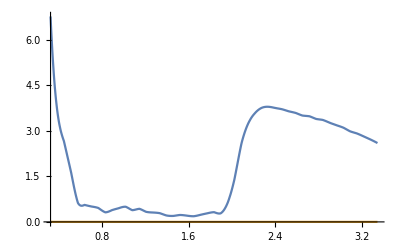

```mathematica
Plot[{Im[eps[x]],Im[epsf[x]]},{x,3.243771454403504*^6,3.3438985136666235*^7}]
```

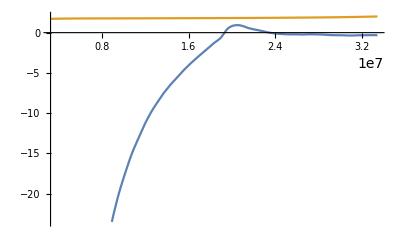

```mathematica
Plot[{Re[eps[x]],Re[epsf[x]]},{x,3.243771454403504*^6,3.3438985136666235*^7}]
```

```mathematica
Plot[{Re[f[x]], Im[f[x]]},{x,3.243771454403504*^6,3.3438985136666235*^7}]
```

-Graphics-

```mathematica
λ1 = 650*10^-9;
λ2 = 1550*10^-9;
k1 = (2*Pi)/λ1;
k2 = (2*Pi)/λ2;
```

```mathematica
Manipulate[Plot[Abs[P[eps[k2],epsf[k2],x,d,k2]]^2,{x,k2*Re[Sqrt[epsf[k2]]],k2*Sqrt[1.5^2]},PlotRange->{0,1}],{d,0,2*5.6571*^-8}];
fig1=Plot[Abs[P[eps[k1],epsf[k1],x,5.5*^-8,k1]]^2,{x,k1*Re[Sqrt[epsf[k1]]],k1*Sqrt[1.5^2]},PlotRange->{0,1}];
fig2=Plot[Abs[P[eps[k2],epsf[k2],x,4.4*^-8,k2]]^2,{x,k2*Re[Sqrt[epsf[k2]]],k2*Sqrt[1.5^2]},PlotRange->{0,1}];
```

Кречманн на 500нм достигается при d = 5.6571*^-8

eps[k2]
epsf[k1]

-129.473+3.22017 ⅈ

1.78223+2.67×10^-9 ⅈ

```mathematica
Plot[Abs[Abs[P[-9.798031497147885+0.31100117404955313 ⅈ,1.782225,x,d,k1]]^2,{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1}}]
```

Кречманн на 1500нм достигается при d = 3.17*^-8

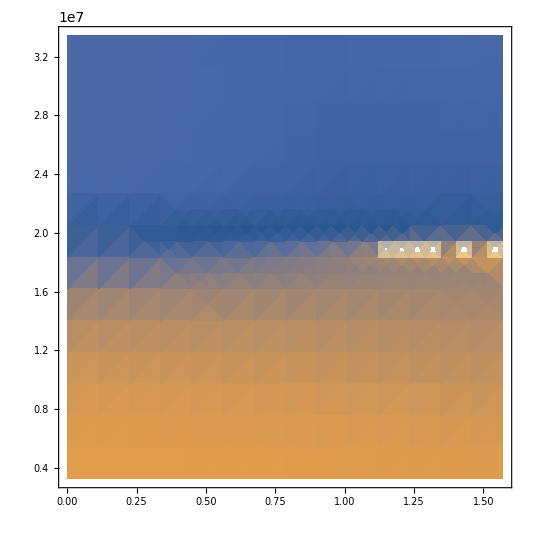

```mathematica
DensityPlot[Abs[P[eps[k],epsf[k],x,3.17*^-8,k]]^2,{x,0,Pi/2},{k,3.243771454403504*^6,3.3438985136666235*^7}]
```

```mathematica
Re[Sqrt[epsf[k2]]]
```

1.31811

```mathematica
fig1data=Cases[fig1,Line[data_]:>data,-4,1][[1]];
```

```mathematica
fig2data = Cases[fig2,Line[data_]:>data,-4,2][[2]];
Export["krechman650nm.csv",fig1data];
Export["krechman1550nm.csv",fig2data];
```

krechman1550nm.csv